# LAB M5: Hooke’s Law

## Introduction:

This lab is based of the idea of Hooke’s Law. The Hooke’s law states that the force exerted by a single spring is directly proportional to the extension/compression of the spring from its equilibrium length (Formula-> F=-kx; k= stiffness of the spring). The main purpose for this lab was to determine the value of k by conducting various experiments.

## Part 1: Measurement of Spring Constant (k)

The main purpose for this part is to determine the value of the spring consant k. This would require a few steps, first the weight of the spring itself would be determined, then the zero position would be measured. In order to accomplish that, the position of the empty tray would be measured. Then the positons of the masses would be measured (by the increments of 50g). Hence, the value of the spring constant would be calculated by dividing the position of each mass by mass * gravity. Thus, the standard deviation, standard deviation of mean, and the average will be calculated for the k values.

Change in position(m) | Weight on spring(N)
0.060 | 0.490
0.123 | 0.980
0.185 | 1.469
0.249 | 1.959
0.311 | 2.449
0.371 | 2.939
0.435 | 3.429
0.498 | 3.918
0.558 | 4.408
0.618 | 4.898

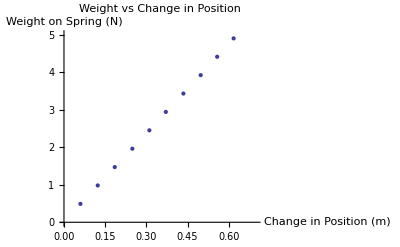

```mathematica
SM=0.1614; (*Mass of the spring (kg)*)
δSM=0.0001;(*Error of the mass of spring *)
EP=0.142;(*Equilibrium point of the spring with no weight (m)*)
M={0.050,0.100,0.150,0.200,0.250,0.300,0.350,0.400,0.450,0.500};(*Masses added to the spring (kg)*)
P={0.202,0.265,0.327,0.391,0.453,0.513,0.577,0.640,0.700,0.760};(*Position in the spring with weight (m)*)
G=9.796; (*Literature value of gravity (m/s^2)*)
W=M*G;(*Formula to determine weight on spring (N)*)
CP=P-EP;(*Formula to determine the change in position for the spring (m)*)
CPvsW=Thread[{CP,W}];
NumberForm[Grid[Prepend[CPvsW,{"Change in position(m)","Weight on spring(N)"}], Frame->All],{10,3}]
ListPlot [{CPvsW}, PlotLabel-> "Weight vs Change in Position", AxesLabel-> {"Change in Position (m)", "Weight on Spring (N)"}, PlotRange->{{0,0.70}, {0,5}}](*Graph of CP vs W*)
```

## Part 2: Measurement of the Period

The second part of the lab’s purpose is to determine the period. In order to achieve that set goal, one needs to divide the measured period of each of the masses by the number of times the spring oscillated. The uncertainty for this would be the human reaction time (0.1 seconds) divided by the number of oscillations (which would be 50). We would also be calculating the effective mass.

```mathematica
M1=0.100; (*Mass of the weight (kg)*)
M2=0.200; (*Mass of the weight (kg)*)
M3= 0.500;(*Mass of the weight (kg)*)
T1=42.64; (*Trial 1 with M1 in seconds (s)*)
T2= 55.10; (*Trial 1 with M2 in seconds (s)*)
T3= 82.21; (*Trial with M3 in seconds (s)*)
f=0.281; (*f value to calculate the effective mass*)
δf=0.002; (*Uncertainity of f*)
δTtotal=0.1; (*human reaction time (s)*)
NO=50; (*Number of oscillations measured*)
T11=42.8;(*Trial 2 with M1 in seconds (s)*)
```

## Data Analysis

Part 1: Measurement of Spring Constant (k)

```mathematica
k= (M*G)/CP;(*calculated spring constants (N/m)*)
kgrid=Thread[{k}];
NumberForm[Grid[Prepend[kgrid,{"Spring Constants (k) (N/m)"}], Frame->All],{10,3}]
kavg=Mean[k]; (*Average of the k values*)
NumberForm[kavg,3]
stdvk=StandardDeviation[k];(*Standard Deviation of K values (N/m)*)
NumberForm[stdvk,3]
stdvkm=stdvk/(√10);(*Calculated standard deviation of mean (error of the mean) (N/m), standard deviation divided by square root of the amount of trials*)
NumberForm[stdvkm,1]
```

Spring Constants (k) (N/m)
8.163
7.964
7.943
7.868
7.875
7.921
7.882
7.868
7.900
7.926

7.93

0.088

0.03

In this part of the lab we calculated the k values for all 10 times, listed above in the table. We then calculated the Kaverage throughout the 10 trials which gave us 7.93 ± 0.03 N/m. Also giving us a standard deviation of 0.088.

Part 2: Measurement of the Period

Masses (1,2,3) (kg) |  Effective Mass (1,2,3)(kg) | Period Measured (1,2,3)(s) | Period Calculated (1,2,3) (s)
0.100 | 0.145 | 0.854 | 0.851
0.200 | 0.245 | 1.102 | 1.105
0.500 | 0.545 | 1.644 | 1.648

Calculated uncertainity in period (s) | Calculated uncertainty in calculated measured period(s) | Discrepency in our measurement vs calculated (s)
0.002 | 0.002 | 0.004
0.002 | 0.002 | 0.003
0.002 | 0.002 | 0.003

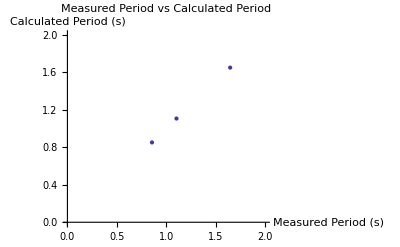

Ratio of the measured period vs calculated period (1,2,3)
1.004
0.997
0.998

```mathematica
Avg1=(T1+T11)/2;(* Average time for trial 1 with Mass 1 (s)*)
Pmeas= {Avg1/NO, T2/NO,T3/NO}; (*Calculates the measured value of Period (s)*)
δP=δTtotal/NO; (*calculated uncertainty in period (s)*)
δPP={δP, δP, δP};
Emeff1=M1+(f*SM);(*Calculated effective mass for M1 (kg)*)
Emeff2=M2+(f*SM);(*Calculated effective mass for M2 (kg)*)
Emeff3=M3+(f*SM);(*Calculated effective mass for M3 (kg)*)
Emeff={Emeff1,Emeff2,Emeff3};
Mpt2={M1,M2,M3};
Mgrid=Thread[{Mpt2,Emeff,Pmeas, Pcal}];
NumberForm[Grid[Prepend[Mgrid,{"Masses (1,2,3) (kg)"," Effective Mass (1,2,3)(kg)","Period Measured (1,2,3)(s)", "Period Calculated (1,2,3) (s)"}], Frame->All],{10,3}]
Pcal=2π √(Emeff/kavg);(*The calculated period (s)*)
δPcal=√((1/2*δSM/Emeff)^2+(1/2*stdvkm/kavg)^2); (*Uncertainity in our calculated period by using the master rule of error propagation*)
Discrep=Abs[Pmeas-Pcal];
Pgrid=Thread[{δPP,δPcal,Discrep}];
NumberForm[Grid[Prepend[Pgrid,{"Calculated uncertainity in period (s)","Calculated uncertainty in calculated measured period(s)","Discrepency in our measurement vs calculated (s)"}], Frame->All],{10,3}]
MPvsCP = Thread[{Pmeas,Pcal}];
ListPlot[{MPvsCP}, PlotLabel -> "Measured Period vs Calculated Period", AxesLabel -> {"Measured Period (s)", "Calculated Period (s)"}, PlotRange -> {{0, 2}, {0, 2}}]
R=Pmeas/Pcal; 
Rgrid=Thread[{R}];
NumberForm[Grid[Prepend[Rgrid,{"Ratio of the measured period vs calculated period (1,2,3)"}], Frame-> All], {10,3}]
```

The ratios are extremely close to the value 1, signifying that the measured period and the calculated periods are proportional to each other. Each of the values were measured for all 3 trials as shown in the above charts.

## Conclusion

Part 1: Measurement of Spring Constant (k)

This lab was conducted to prove the idea and/or concept behind the Hooke’s Law. This part in particular focused on calculating the spring constant K (N/m). Hence, the average k value (since many trials were done) was computed to be 7.93 ± 0.03 N/m. Certain limitations for this part could be that the measurement of the zero position correctly. It was also pretty hard to measure the exact position of the spring + weight, as in my partner measured it 0.01cm off than what I determined the position to be, thus a human error played in a huge role in the error for this part of the lab. There could also have been small amount of friction when the spring was attached to a rod of wood on the top, while we were measuring the positions. Room temperature could also cause the physical quality of the metal of the spring. In order to improve this lab, a machine should be used to measure the position instead of the human being that is conducting the experiment allowing to give a more accurate data.

Part 2: Measurement of the Period

This part in particular focused on the comparison between the measured value of periods with the theoretical values. Hence, we recorded the amount of time for several masses on the spring to complete 50 oscillations. Thus the measured period would be the time taken divided by the amount of oscillations. On the other hand, the theoretical period was calculated using the K values calculated from the first part and the effective mass. The effective mass is the mass on the spring added to the product of f and mass of the spring. Then the uncertainty was calculated by using the master rule of error propagation. The calculated values for the calculated period and measured periods with respect to the masses has already been shown in the data analysis. Hence, each calculated period was compared to the measured period, creating a graph. Since the ratio between those two is extremely close to 1, meaning the slope for the function to 1, it implies that the best fit line for this part was y=x. All the data points were extremely close to the value of 1, giving us proof that the ratio was right. However, there was a tiny bit of error since they were not exactly at the ratio of 1. The error could've been from not accurately recording the time with respect to the oscillations. In addition to that error, friction also played a part in it as a limitation due to the spring being attached to the wood thus creating friction and error in the data. Most importantly, air resistance could also play a part in limitation. To improve this part of the lab everything should be done digitally, even when letting the mass go from a certain angle, for safety reasons and accuracy reasons.